# Combinatorics

This paclet is for the study of combinatorics. I am a combinatorialist. That means I study combinatorics.

The functions defined in the PeterBurbery`Combinatorics` context provide support for finding solutions to combinatorics-related problems.

```mathematica
Needs["PeterBurbery`Combinatorics`"]
```

## Indexes

PermutationIndex[perm] | gives the lexicographic index of permutation perm.
PermutationFromIndex[index,lengthInput] | returns the permutation of length lengthInput corresponding to the indexth permutation in lexicographic order.
SubsetIndex[list] | gives the index of subset list.
SubsetFromIndex[index,len] | returns a subset of length len with given index.

Computing the index or using the index to get the thing.

Find the index of a random permutation

```mathematica
PermutationIndex[Echo[PermutationList@RandomPermutation[9]]]
```

{2,6,9,1,4,8,3,5,7}

64843

Get the permutation:

```mathematica
PermutationFromIndex[%,9]
```

{2,6,9,1,4,8,3,5,7}

Here's a neat application of this function. We can use this to solve Project Euler Problem 24 Lexicographic Permutations. What is the millionth lexicographic permutation of the digits 0, 1, 2, 3, 4, 5, 6, 7, 8, and 9?

```mathematica
PermutationFromIndex[1000000(*a million is 10^6*), 10(*because Length[{0,1,2,3,4,5,6,7,8,,9}] is 10, not 9*)]
```

{3,8,9,4,10,2,6,5,7,1}

Now we need to subtract 1. 10 will become 9 and 1 will become 0.

```mathematica
PermutationFromIndex[1000000(*a million is 10^6*), 10(*because Length[{0,1,2,3,4,5,6,7,8,,9}] is 10, not 9*)]-1
```

{2,7,8,3,9,1,5,4,6,0}

Now we can use FromDigits.

```mathematica
FromDigits[PermutationFromIndex[1000000(*a million is 10^6*), 10(*because Length[{0,1,2,3,4,5,6,7,8,,9}] is 10, not 9*)]-1]
```

2783915460

And that's the answer!

Find a subset's index.

```mathematica
SubsetIndex[{2,4,6}]
```

29

Find the subset.

```mathematica
SubsetFromIndex[29,3]
```

{2,4,6}

Compute the central binomial coefficient.

```mathematica
CentralBinomialCoefficient[54]
```

24857784491537440929618523018320

```mathematica
CentralBinomialCoefficient[n]
```

Binomial[2 n,n]

Find the generating function.

```mathematica
GeneratingFunction[CentralBinomialCoefficient[n],n,x]
```

1/(√(1-4 x))

Make a table of values.

```mathematica
Dataset[AssociationMap[<|"n"->CentralBinomialCoefficient[#]|>&][Range[21]]]
```

The digits of (2 10^n
10^n) for n=0, 1, … are

```mathematica
Dataset[AssociationMap[<|"n"->IntegerLength[CentralBinomialCoefficient[10^#]]|>&][Range[0,8]]]
```

These digits are converging to the digits of log_10 4.

```mathematica
N[Log[10,4],40]
```

0.6020599913279623904274777894489860535364

Let's look at the modified central binomial coefficient.

```mathematica
Dataset[AssociationMap[<|"n"->ModifiedCentralBinomialCoefficient[#]|>&][Range[0,21]]]
```

The generating function is  (1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)).

```mathematica
SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,9-1}]
```

126

This matches our output.

```mathematica
Dataset[AssociationMap[<|"n"->ModifiedCentralBinomialCoefficient[#],"seriesCoefficient"->SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}],"equal"->ModifiedCentralBinomialCoefficient[#]===SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}]|>&][Range[0,21]]]
```

If we start at 1, we will get all True instead of a False at 0.

```mathematica
Dataset[AssociationMap[<|"n"->ModifiedCentralBinomialCoefficient[#],"seriesCoefficient"->SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}],"equal"->ModifiedCentralBinomialCoefficient[#]===SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}]|>&][Range[2,21]]]
```

For more details, please visit A001405 on the OEIS.

Make a random multiset of the hazel color rainbow palette.

```mathematica
hazelRainbowPalette=Table[LUVColor[RGBColor["#"<>color]],{color,{"c9c789","94c989","89c9b5","89a7c9","c989b9","c99089"}}]
```

{LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785]}

```mathematica
randomMultiset=RandomChoice[hazelRainbowPalette,21]
```

{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595]}

Count the derangements.

```mathematica
EnumerateMultisetPartialDerangements[randomMultiset]
```

77589925224

This is the same as having 0 fixed points.

```mathematica
EnumerateMultisetPartialDerangements[randomMultiset,0]
```

77589925224

Count partial derangements with 3 fixed points.

```mathematica
EnumerateMultisetPartialDerangements[randomMultiset,3]
```

1281427641738

Let's do a smaller example. This time, let's list all the elements of the set.

```mathematica
hazelRainbowPaletteSubset=RandomSample[hazelRainbowPalette,4]
```

{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595]}

```mathematica
subsetRandomMultiset=RandomChoice[hazelRainbowPaletteSubset,{7}]
```

{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595]}

Let's find all the multiset partial derangements.

```mathematica
MultisetPartialDerangements[subsetRandomMultiset]
```

{{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]}}

Here is the count.

```mathematica
EnumerateMultisetPartialDerangements[subsetRandomMultiset]
```

30

If we compute partials derangements with 3 fixed points, we will get 101 elements.

```mathematica
EnumerateMultisetPartialDerangements[subsetRandomMultiset,3]
```

101

I will limit the output to 20 this time.

```mathematica
MultisetPartialDerangements[subsetRandomMultiset,3,20]
```

{{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]},{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]}}

There are ten candies: licorice, peppermint drops, lemon drops, truffles, gummy bears, gummy worms, chocolate bars, jelly beans, peanut butter cups, and marshmallows. There are four children named Peter, James, John, and Andrew. How many ways can the ten candies be distributed among the four children? We can compute 10 multichoose 4.

```mathematica
Multichoose[10,4]
```

715

Another way of entering it is like this.

```mathematica
10~Multichoose~4
```

715

We can also generate all the combinations and count them. Since there are a lot of combinations, I am not listing them all here and then using Length. I'm just going to use Length immediately.

```mathematica
Length@OrderlessCombinations[{"licorice","peppermint drops","lemon drops","truffles","gummy bears","gummy worms","chocolate bars","jelly beans","peanut butter cups","marshmallows"},{4}]
```

715

Get length four sets from a list of length two:

```mathematica
OrderlessCombinations[Range[2],{4}]
```

{{1,1,1,1},{1,1,1,2},{1,1,2,2},{1,2,2,2},{2,2,2,2}}

Elements need not be integers:

```mathematica
OrderlessCombinations[{"dog","cat","bird"},3]
```

{{bird},{cat},{dog},{bird,bird},{bird,cat},{bird,dog},{cat,cat},{cat,dog},{dog,dog},{bird,bird,bird},{bird,bird,cat},{bird,bird,dog},{bird,cat,cat},{bird,cat,dog},{bird,dog,dog},{cat,cat,cat},{cat,cat,dog},{cat,dog,dog},{dog,dog,dog}}

We could consider {"cat", "cat", "cat"} and {"dog", "dog", "dog"} as partly equal.

```mathematica
CanonicalMultiset[{"cat","cat","cat"}]
```

{1,1,1}

```mathematica
CanonicalMultiset[{"dog","dog","dog"}]
```

{1,1,1}

If we delete duplicates by CanonicalMultiset, we get fewer elements.

```mathematica
DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]
```

{{bird},{bird,bird},{bird,cat},{bird,bird,bird},{bird,bird,cat},{bird,cat,cat},{bird,cat,dog}}

```mathematica
CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]
```

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

Here's what we would get something like.

```mathematica
OrderlessCombinationsOfUnmarkedElements[{"dog","cat","bird"},3]
```

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

These produce the same output.

```mathematica
CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]
```

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

Let's compare the performance for a large set.

```mathematica
ResourceFunction["EchoPerformance"][CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]]
```

Map  {0.0005623 s,7168 B}

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
ResourceFunction["EchoPerformance"][OrderlessCombinationsOfUnmarkedElements[{"dog","cat","bird"},3]]
```

OrderlessCombinationsOfUnmarkedElements  {0.0003973 s,7280 B}

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
ResourceFunction["EchoPerformance"][CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},7]];]
```

CompoundExpression  {0.0026763 s,40688 B}

```mathematica
ResourceFunction["EchoPerformance"][OrderlessCombinationsOfUnmarkedElements[{"dog","cat","bird"},7];]
```

CompoundExpression  {0.0021079 s,40272 B}

The definition of the function is significantly faster and uses significantly less memory.

```mathematica
ResourceFunction["EchoPerformance"][CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[RandomWord["Noun",7],17]];]
```

CompoundExpression  {16.5169 s,148109320 B}

```mathematica
ResourceFunction["EchoPerformance"][OrderlessCombinationsOfUnmarkedElements[RandomWord["Noun",7],17];]
```

CompoundExpression  {9.02953 s,84408424 B}

Make a Ferrers diagram for every partition of 5.

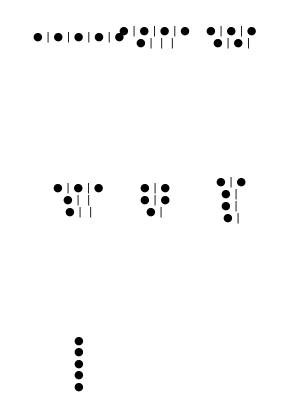

```mathematica
GraphicsGrid[Partition[FerrersDiagram/@IntegerPartitions[5],UpTo[3]]]
```

Rows 1 to 4 have 5, 4, 2, 2 dots:

```mathematica
FerrersDiagram[{5,4,2,2}]
```

● | ● | ● | ● | ●
● | ● | ● | ● | 
● | ● |  |  | 
● | ● |  |  |

Here is a random choice of one of the 204226 partitions of 50:

```mathematica
Framed@FerrersDiagram@RandomChoice[IntegerPartitions@50]
```

● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
● | ● | ● | ● | ● | ● |  |  |  |  | 
● | ● | ● | ● | ● | ● |  |  |  |  | 
● | ● | ● |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  |

Select from the list {5,6,7,8,9} those permutations that form a prime when concatenating the digits:

```mathematica
SelectPermutations[{5,6,7,8,9},PrimeQ@*FromDigits]
```

{{5,6,8,9,7},{5,7,6,8,9},{5,8,6,7,9},{5,8,9,6,7},{6,5,7,8,9},{6,7,5,8,9},{6,8,5,9,7},{6,9,8,5,7},{7,5,6,8,9},{7,5,8,6,9},{7,8,5,6,9},{8,6,5,7,9},{8,9,5,6,7},{8,9,6,5,7},{9,6,5,8,7},{9,6,8,5,7}}

Here are the numbers.

```mathematica
FromDigits/@SelectPermutations[{5,6,7,8,9},PrimeQ@*FromDigits]
```

{56897,57689,58679,58967,65789,67589,68597,69857,75689,75869,78569,86579,89567,89657,96587,96857}

Select permutations of length 3:

```mathematica
SelectPermutations[{5,6,7,8,9},{3},PrimeQ@*FromDigits]
```

{{5,6,9},{5,8,7},{6,5,9},{7,6,9},{8,5,7},{8,5,9},{9,6,7}}

Here are the numbers.

```mathematica
FromDigits/@SelectPermutations[{5,6,7,8,9},{3},PrimeQ@*FromDigits]
```

{569,587,659,769,857,859,967}

Select permutations with length 3—4:

```mathematica
SelectPermutations[{5,6,7,8,9},{3,4},PrimeQ@*FromDigits]
```

{{5,6,9},{5,8,7},{6,5,9},{7,6,9},{8,5,7},{8,5,9},{9,6,7},{5,6,8,9},{5,8,6,7},{5,8,6,9},{5,8,7,9},{5,8,9,7},{5,9,8,7},{6,8,5,7},{7,5,8,9},{8,5,9,7},{9,5,8,7},{9,8,5,7}}

Here are the numbers.

```mathematica
FromDigits/@SelectPermutations[{5,6,7,8,9},{3,4},PrimeQ@*FromDigits]
```

{569,587,659,769,857,859,967,5689,5867,5869,5879,5897,5987,6857,7589,8597,9587,9857}

Select permutations for which the first two elements and the last elements add up to the same value:

```mathematica
SelectPermutations[{1,2,3,4},Total[#[[1;;2]]]==Total[#[[3;;4]]]&]
```

{{1,4,2,3},{1,4,3,2},{2,3,1,4},{2,3,4,1},{3,2,1,4},{3,2,4,1},{4,1,2,3},{4,1,3,2}}

Select the first ten permutations of length 4 for which the elements add up to an odd number:

```mathematica
SelectPermutations[{1,2,3,4,5,6},{4},OddQ@*Total,10]
```

{{1,2,3,5},{1,2,4,6},{1,2,5,3},{1,2,6,4},{1,3,2,5},{1,3,4,5},{1,3,5,2},{1,3,5,4},{1,3,5,6},{1,3,6,5}}

Select polynomials for which the slope is 1 at x=0:

```mathematica
out=Total/@SelectPermutations[{x,4x,1,(x-2)^2},4,((D[Total[#],x])/.x->0)==1&]
```

{x,1+x,1+x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x}

Expand the polynomials.

```mathematica
Expand[out]
```

{x,1+x,1+x,4+x+x^2,4+x+x^2,4+x+x^2,4+x+x^2,4+x+x^2,4+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2}

There are really only three unique ones.

```mathematica
DeleteDuplicates[Expand[out]]
```

{x,1+x,4+x+x^2,5+x+x^2}

Make a graph of all of them.

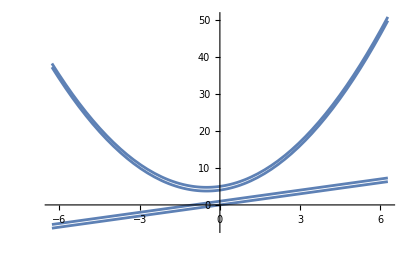

```mathematica
Plot[DeleteDuplicates[Expand[out]],{x,-2Pi,2Pi},PlotLegends->"Expressions"]
```

Confirm that the slope is indeed unity at x=0:

```mathematica
D[#,x]/.x->0&/@out
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Duplicated items are treated the same:

```mathematica
SelectPermutations[{6,7,7,7,8},{2},(Total[#]==14)&]
```

{{6,8},{7,7},{8,6}}

The main difference between SelectPermutations[list,crit] and Select[Permutations[list],crit] is the memory usage:

```mathematica
MaxMemoryUsed[result1=SelectPermutations[Range[3,13],6,Total[#]==24&];]
```

76800

Using Select and Permutations uses 500 times more memory:

```mathematica
MaxMemoryUsed[result2=Select[Permutations[Range[3,13],6],Total[#]==24&];]
```

37563192

Verify that the results are identical:

```mathematica
result1==result2
```

True

Head does not have to be List:

```mathematica
SelectPermutations[f[1,2,3,4,5],{2},((Plus@@#)==6&)]
```

{f[1,5],f[2,4],f[4,2],f[5,1]}

SelectPermutations might take longer as it is written in higher-level code as compared to the implementation of Permutations:

```mathematica
MaxMemoryUsed[time=AbsoluteTiming[result1=SelectPermutations[Range[3,13],6,Total[#]==24&];][[1]]];
Grid[{{"Time [sec]:",time},{"Memory usage [bytes]:",%}}]
```

Time [sec]: | 3.14873
Memory usage [bytes]: | 76800

Using the built-in functions is faster at the expense of 500× more memory:

```mathematica
MaxMemoryUsed[time=AbsoluteTiming[result2=Select[Permutations[Range[3,13],6],Total[#]==24&];][[1]]];
Grid[{{"Time [sec]:",time},{"Memory usage [bytes]:",%}}]
```

Time [sec]: | 0.898735
Memory usage [bytes]: | 37562680

Select subsets from {1,2,3,4,5} that add up to 10:

```mathematica
SelectSubsets[{1,2,3,4,5},EqualTo[10]@*Total]
```

{{1,4,5},{2,3,5},{1,2,3,4}}

Select subsets of length 2 to 4 that sum up to a prime:

```mathematica
SelectSubsets[{1,2,3,4,5},{2,4},PrimeQ@*Total]
```

{{1,2},{1,4},{2,3},{2,5},{3,4},{1,2,4},{2,4,5},{1,2,3,5},{1,3,4,5}}

Select all subsets of length 2 that add up to 6:

```mathematica
SelectSubsets[{1,2,3,4,5},{2},EqualTo[6]@*Total]
```

{{1,5},{2,4}}

Select all subsets that add up to 0:

```mathematica
SelectSubsets[{-3,-2,-1,0,1,2,3},All,EqualTo[0]@*Total]
```

{{},{0},{-3,3},{-2,2},{-1,1},{-3,0,3},{-3,1,2},{-2,-1,3},{-2,0,2},{-1,0,1},{-3,-2,2,3},{-3,-1,1,3},{-3,0,1,2},{-2,-1,0,3},{-2,-1,1,2},{-3,-2,0,2,3},{-3,-1,0,1,3},{-2,-1,0,1,2},{-3,-2,-1,1,2,3},{-3,-2,-1,0,1,2,3}}

Select all subsets of odd length that add up to a prime:

```mathematica
SelectSubsets[{-3,-2,-1,0,1,2,3},{1,7,2},PrimeQ@*Total]
```

{{-3},{-2},{2},{3},{-3,-2,0},{-3,-2,2},{-3,-2,3},{-3,-1,1},{-3,-1,2},{-3,0,1},{-3,2,3},{-2,-1,0},{-2,-1,1},{-2,1,3},{-2,2,3},{-1,0,3},{-1,1,2},{-1,1,3},{0,1,2},{0,2,3},{-3,-2,-1,0,1},{-3,-2,-1,0,3},{-3,-2,-1,1,2},{-3,-2,-1,1,3},{-3,-2,0,1,2},{-3,-1,1,2,3},{-3,0,1,2,3},{-2,-1,0,2,3},{-2,-1,1,2,3},{-1,0,1,2,3}}

Select the first 8 subsets that add up to a prime:

```mathematica
SelectSubsets[{1,2,3,4,5},All,PrimeQ@*Total,8]
```

{{2},{3},{5},{1,2},{1,4},{2,3},{2,5},{3,4}}

Find subsets that add up to 25:

```mathematica
SelectSubsets[Range[6,13],All,EqualTo[25]@*Total]
```

{{12,13},{6,7,12},{6,8,11},{6,9,10},{7,8,10}}

The main difference between Select and Subsets, and SelectSubsets is the amount of memory used:

```mathematica
MaxMemoryUsed[res1=SelectSubsets[Range[6,24],EqualTo[25]@*Total]]
```

62528

Compared to naive implementation, which requires roughly a 1000 times more memory:

```mathematica
MaxMemoryUsed[res2=Select[Subsets[Range[6,24]],EqualTo[25]@*Total]]
```

65071816

Verify the result is the same:

```mathematica
res1===res2
```

True

With a criterion that is a tautology, SelectSubsets and Subsets give the same results:

```mathematica
SelectSubsets[Range[5],True&]==Subsets[Range[5]]
```

True

SelectSubsets might not be able to return the number of elements that are requested:

```mathematica
SelectSubsets[Range[5],All,EqualTo[8]@*Total,5]
```

{{3,5},{1,2,5},{1,3,4}}

Find subsets that add up to 0:

```mathematica
sets=SelectSubsets[Range[-7,7],All,EqualTo[0]@*Total];
Short[sets]
```

{{},{0},«1517»,{-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7}}

Visualize the lengths of the lists:

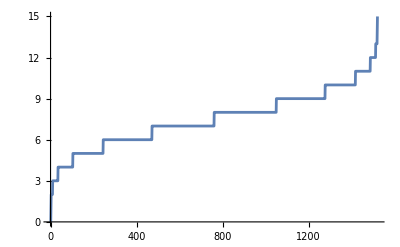

```mathematica
ListPlot[Length/@sets,Joined->True]
```

Find out for which 2-tuple the sum is a prime:

```mathematica
SelectTuples[Range[10],2,PrimeQ@*Total]
```

{{1,1},{1,2},{1,4},{1,6},{1,10},{2,1},{2,3},{2,5},{2,9},{3,2},{3,4},{3,8},{3,10},{4,1},{4,3},{4,7},{4,9},{5,2},{5,6},{5,8},{6,1},{6,5},{6,7},{7,4},{7,6},{7,10},{8,3},{8,5},{8,9},{9,2},{9,4},{9,8},{9,10},{10,1},{10,3},{10,7},{10,9}}

Only get the first five:

```mathematica
SelectTuples[Range[10],2,PrimeQ@*Total,5]
```

{{1,1},{1,2},{1,4},{1,6},{1,10}}

Find the first 15 three-letter palindromic lists:

```mathematica
SelectTuples[CharacterRange["a","e"],3,PalindromeQ@*StringJoin,15]
```

{{a,a,a},{a,b,a},{a,c,a},{a,d,a},{a,e,a},{b,a,b},{b,b,b},{b,c,b},{b,d,b},{b,e,b},{c,a,c},{c,b,c},{c,c,c},{c,d,c},{c,e,c}}

Find vectors for which the norm is an integer:

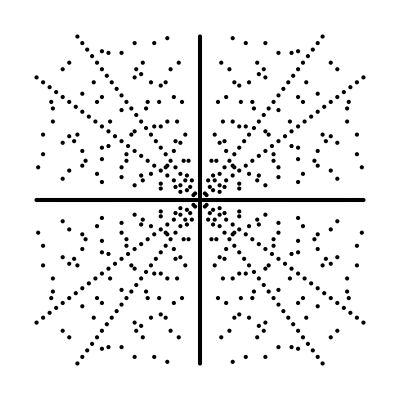

```mathematica
SelectTuples[Range[-100,100],2,IntegerQ@*Norm]//Point//Graphics
```

The main difference between Select and Tuples and SelectTuples is the amount of memory used:

```mathematica
MaxMemoryUsed[SelectTuples[Range[10],5,EqualTo[30]@*Total]]
```

1049416

Compared to naive implementation:

```mathematica
MaxMemoryUsed[Select[Tuples[Range[10],5],EqualTo[30]@*Total]]
```

21711208

The length of the results might be smaller than the argument m:

```mathematica
SelectTuples[{-1,0,1},3,EqualTo[1]@*Norm,10]
```

{{-1,0,0},{0,-1,0},{0,0,-1},{0,0,1},{0,1,0},{1,0,0}}

I got kind of confused with this.

Combinatorica's Eulerian[n,k] gives the number of permutations of length n with k runs.

This function uses a different index for k.

If you have EulerianNumber[n,k], do Eulerian[n,k-1].

If you have Eulerian[n,k], do EulerianNumber[n,k+1].

This also affects the definition of other related functions like EulerianCatalanNumber.

One interpretation of the Eulerian Catalan number is "Twice the number of permutations of {1,2,...,2n} with n ascents".

```mathematica
Dataset[AssociationMap[<|"n"->EulerianCatalanNumber[#]|>&][Range[0,21]]]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/tutorial/Combinatorics

### Keywords